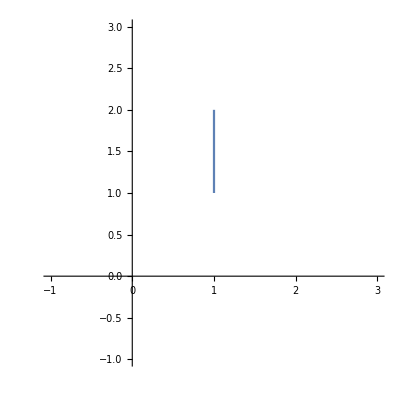

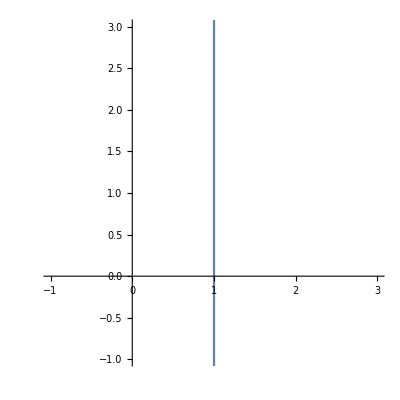

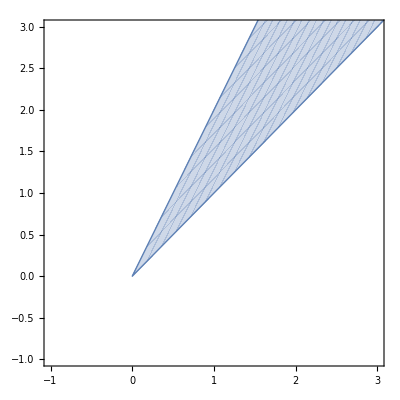

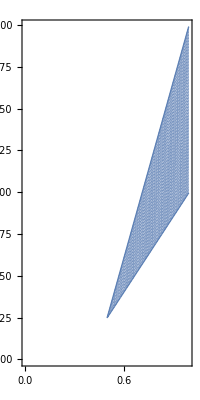

```mathematica
ClearAll[conv, affine, conic, p1a, p1a,p3a]
conv[{x1_, x2_}] := ParametricPlot[theta x1 + (1-theta)x2,{theta,0,1}, PlotRange->{{-1,3},{-1,3}}
];
affine[{x1_, x2_}] := ParametricPlot[theta x1 + (1-theta)x2,{theta,-100,100}, PlotRange->{{-1,3},{-1,3}}
];
conic[{x1_, x2_}] := ParametricPlot[alpha x1 + beta x2,{alpha,0,10}, {beta,0,10}, PlotRange->{{-1,3},{-1,3}}
];



conv[{x1_, x2_,x3_}] := ParametricPlot[
Boole[alpha + beta ≤ 1](alpha x1 + beta x2 + (1-alpha-beta) x3),
{alpha,0,1},
{beta,0,1}(*,
 PlotRange->{{0.25,1.25},{-0.5,2.25}}*)
];
affine[{x1_, x2_,x3_}] := Show[
Table[
ParametricPlot[
Boole[alpha + beta +gamma == 1](alpha x1 + beta x2 + gamma x3),
{alpha,-10,10},
{beta,-10,10}
],
{gamma,-10,10,0.1}
]
,
PlotRange->All
]
ptsA = {{1,1},{1,2}};
ptsB = {{1,1},{1,2},{0.5,0.25}};
paConv = conv[ptsA]
paAffine = affine[ptsA]
paConic = conic[ptsA]
pbConv = conv[ptsB]
(*pbAffine = affine[ptsB]*)
```

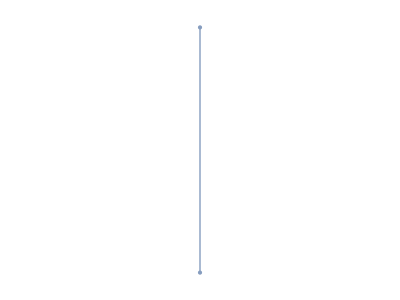

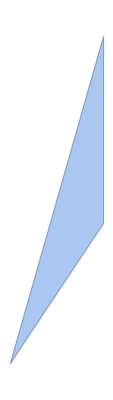

```mathematica
ConvexHullMesh[ptsA]
ConvexHullMesh[ptsB]
```

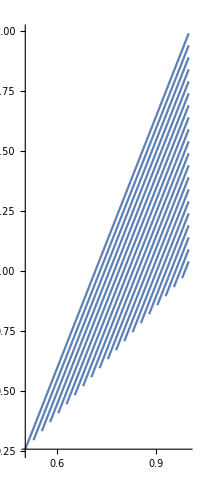

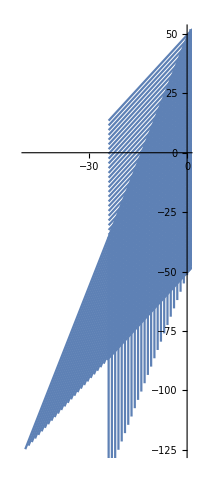

```mathematica
ClearAll[x1,x2,x3, alpha, beta]
{x1,x2,x3} = ptsB;
Show[
Table[ 
ParametricPlot[ alpha x1 + beta x2 + (1-alpha - beta)x3,{beta,0,1-alpha}],{alpha,0.01,1,0.05}
 ]
]
Module[{r=50,d = 2 r / 10},Show[{
Table[ 
ParametricPlot[ alpha x1 + beta x2 + (1-alpha - beta)x3,{beta,-r,r}],{alpha,-r,r,d}
 ],
Table[ 
ParametricPlot[ alpha x2 + beta x3 + (1-alpha - beta)x1,{beta,-r,r}],{alpha,-r,r,d}
 ],
Table[ 
ParametricPlot[ alpha x3 + beta x1 + (1-alpha - beta)x2,{beta,-r,r}],{alpha,-r,r,d}
 ]}
]
]
```

```mathematica
|
```